```mathematica
(* Differential Equations, Homework 3 *)
```

```mathematica
(* Qs 1b *)

ClearAll["Global`*"];
```

```mathematica
A[t_]={{1+2Cos[2t],1-2Sin[2t]},{-(1+2Sin[2t]),1-2Cos[2t]}};
```

```mathematica
Q[t_]={{Cos[t],Sin[t]},{-Sin[t],Cos[t]}};

Mat=TrigReduce[Inverse[Q[t]].(A[t].Q[t]-Q'[t])]
```

{{3,0},{0,-1}}

```mathematica
(* -------------------------------------------------------- *)

(* Qs 1c *)
```

```mathematica
ClearAll["Global`*"];
```

```mathematica
DSolve[x2'[t]==x2[t]+2*C1*(Sin[t]+2)*Exp[t], x2[t], t]
```

{{x2[t]→ⅇ^t C[1]+ⅇ^t (4 C1 t-2 C1 Cos[t])}}

```mathematica
U[t_]={{(1/2)*(Sin[t]+2),0},{2t-Cos[t]+1,1}};

W[t_]={{(1/2)*(Sin[t]+2),0},{-Cos[t]+1,1}};
```

```mathematica
TrigReduce[Inverse[W[t]].U[t]]
```

{{1,0},{2 t,1}}

```mathematica
V[t_]={{Exp[t],0},{2*Exp[t]+2t*Exp[t],Exp[t]}};
Z[t_]={{Exp[t],0},{2t*Exp[t],Exp[t]}};
```

```mathematica
FullSimplify[V[t].Inverse[Z[t]]]
```

{{1,0},{2,1}}

```mathematica
(* -------------------------------------------------------- *)
```

```mathematica
(* Qs 3 *)

(* n=1 *)

ClearAll["Global`*"];

q0[t_]=A0*Cos[t]+B0*Sin[t];

f1[t]=-2*μ1*q0'[t]-(δ1+Cos[t]+Sin[2t])*q0[t];
```

```mathematica
qew1=TrigReduce[DSolveValue[q1''[t]+q1[t]==f1[t],q1[t],t]];
```

```mathematica
Coefficient[qew1,(t Cos[t]),1]
Coefficient[qew1,(t Sin[t]),1]
```

1/48 (12 A0+24 B0 δ1-48 A0 μ1)

1/48 (-12 B0-24 A0 δ1-48 B0 μ1)

```mathematica
F1=12*A0+24*B0*δ1-48*A0*Sqrt[μ1square];
F2=-12*B0-24*A0*δ1-48*B0*Sqrt[μ1square];
```

```mathematica
Solve[F1==0&&F2==0,{A0,μ1square}]
```

{{A0→(-B0-√(B0^2-4 B0^2 δ1^2))/(2 δ1),μ1square→1/16 (1-4 δ1^2)},{A0→(-B0+√(B0^2-4 B0^2 δ1^2))/(2 δ1),μ1square→1/16 (1-4 δ1^2)}}

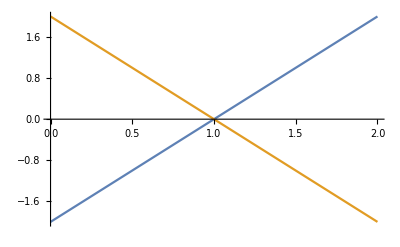

```mathematica
Plot[{2(δ-1), -2(δ-1)},{δ,0,2}]
```

```mathematica
(* -------------------------------------------------------- *)
```

```mathematica
(* n=2 *)

ClearAll["Global`*"];

q0[t_]=A0*Cos[2t]+B0*Sin[2t];
```

```mathematica
f1[t]=-2*μ1*q0'[t]-(δ1+Cos[t]+Sin[2t])*q0[t];

qew1=TrigReduce[DSolveValue[q1''[t]+4q1[t]==f1[t],q1[t],t]];

Coefficient[qew1,(t Cos[2t]),1]
Coefficient[qew1,(t Sin[2t]),1]
```

1/240 (60 B0 δ1-240 A0 μ1)

1/240 (-60 A0 δ1-240 B0 μ1)

```mathematica
F1=60*B0*δ1-240*A0*Sqrt[μ1square];
F2=-60*A0*δ1-240*B0*Sqrt[μ1square];

Solve[F1==0&&F2==0,{A0,μ1square}]
```

{{A0→-ⅈ B0,μ1square→-δ1^2/16},{A0→ⅈ B0,μ1square→-δ1^2/16}}

```mathematica
q1[t_]=1/240 (-30 B0-40 A0 Cos[t]+240 Cos[2 t]+24 A0 Cos[3 t]-10 B0 Cos[4 t]-40 B0 Sin[t]+240 Sin[2 t]+24 B0 Sin[3 t]+10 A0 Sin[4 t]);
```

```mathematica
f2[t]=(Cos[t]+Sin[2t])*q1[t]-2*μ2*q0'[t]-δ2*q0[t];
```

```mathematica
qew2=TrigReduce[DSolveValue[q2''[t]+4q2[t]==f2[t],q2[t],t]];
```

```mathematica
Coefficient[qew2,(t Cos[2t]),1]
Coefficient[qew2,(t Sin[2t]),1]
```

(5544 B0+40320 B0 δ2-161280 A0 μ2)/161280

(-504 A0-40320 A0 δ2-161280 B0 μ2)/161280

```mathematica
F1=5544 B0+40320 B0 δ2-161280 A0 *Sqrt[μ2square];
```

```mathematica
F2=-504 A0-40320 A0 δ2-161280 B0*Sqrt[μ2square];

Solve[F1==0&&F2==0,{A0,μ2square}]
```

{{A0→-(√(-11 B0^2-80 B0^2 δ2))/(√(1+80 δ2)),μ2square→(-11-960 δ2-6400 δ2^2)/102400},{A0→(√(-11 B0^2-80 B0^2 δ2))/(√(1+80 δ2)),μ2square→(-11-960 δ2-6400 δ2^2)/102400}}

```mathematica
Factor[6400 δ2^2+960 δ2+11]
```

(1+80 δ2) (11+80 δ2)

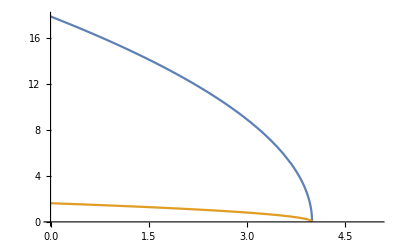

```mathematica
Plot[{4Sqrt[5]Sqrt[4-δ], (4/11)Sqrt[5]Sqrt[4-δ]},{δ,0,5}]
```

```mathematica
(* -------------------------------------------------------- *)
```

```mathematica
(* n=0 *)
```

```mathematica
ClearAll["Global`*"];
```

```mathematica
f1[t_]=-(δ1+Cos[t]+Sin[2t])*A0;
```

```mathematica
DSolveValue[q1''[t]==f1[t],q1[t],t]
```

-1/2 A0 t^2 δ1+C[1]+t C[2]+A0 Cos[t]+1/4 A0 Sin[2 t]

```mathematica
qew1[t_]=A0 Cos[t]+1/4 A0 Sin[2 t]+A1;
```

```mathematica
f1[t_]=-(Cos[t]+Sin[2t])*A0;
```

```mathematica
f2[t_]=-2*μ1*qew1'[t]-(Cos[t]+Sin[2t])*qew1[t]-μ1^2*A0-δ2*A0;
```

```mathematica
qew2=TrigReduce[DSolveValue[q2''[t]==f2[t],q2[t],t]]
```

1/1152(-360 A0 t^2-576 A0 t^2 δ2-576 A0 t^2 μ1^2+1152 C[1]+1152 t C[2]+1152 A1 Cos[t]+144 A0 Cos[2 t]+288 A0 μ1 Cos[2 t]-9 A0 Cos[4 t]+720 A0 Sin[t]-2304 A0 μ1 Sin[t]+288 A1 Sin[2 t]+80 A0 Sin[3 t])

```mathematica
Coefficient[qew2,(t),1]
Coefficient[qew2,(t^2),1]
```

C[2]

(-360 A0-576 A0 δ2-576 A0 μ1^2)/1152

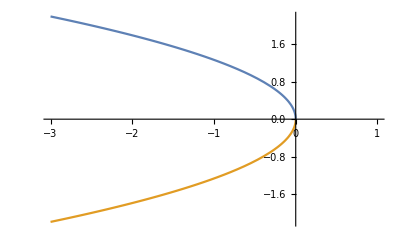

```mathematica
Plot[{Sqrt[(-8/5)*δ],-Sqrt[(-8/5)*δ]},{δ,-3,1}]
```

```mathematica
(* -------------------------------------------------------- *)

(* something *)

Solve[ρ^2-ρ(Cos[w*t]+w*Cos[w*t])+w==0,{ρ}]
```

{{ρ→1/2 (Cos[t w]+w Cos[t w]-√(-4 w+(-Cos[t w]-w Cos[t w])^2))},{ρ→1/2 (Cos[t w]+w Cos[t w]+√(-4 w+(-Cos[t w]-w Cos[t w])^2))}}

```mathematica
(* -------------------------------------------------------- *)
```

```mathematica
(* Qs 6 *)
```

```mathematica
ClearAll["Global`*"];
```

```mathematica
X1[t_]={{Cos[SubPlus[ω] t],Sin[SubPlus[ω] t]/SubPlus[ω]},{-SubPlus[ω]Sin[SubPlus[ω] t],Cos[SubPlus[ω] t]}};
```

```mathematica
X2[t]={{Cos[SubMinus[ω] t],Sin[SubMinus[ω] t]/SubMinus[ω]},{-SubMinus[ω]Sin[SubMinus[ω] t],Cos[SubMinus[ω] t]}};
```

```mathematica
X[t_]=X2[t].X1[π/2];
```

```mathematica
B=X[π/2]
```

{{Cos[(π ω_-)/2] Cos[(π ω_+)/2]-(Sin[(π ω_-)/2] Sin[(π ω_+)/2] ω_+)/(ω_-),(Cos[(π ω_+)/2] Sin[(π ω_-)/2])/(ω_-)+(Cos[(π ω_-)/2] Sin[(π ω_+)/2])/(ω_+)},{-Cos[(π ω_+)/2] Sin[(π ω_-)/2] ω_--Cos[(π ω_-)/2] Sin[(π ω_+)/2] ω_+,Cos[(π ω_-)/2] Cos[(π ω_+)/2]-(Sin[(π ω_-)/2] Sin[(π ω_+)/2] ω_-)/(ω_+)}}

```mathematica
Solve[Det[B-IdentityMatrix[2]*ρ]==0,ρ];
```

```mathematica
(* -------------------------------------------------------- *)
```

```mathematica
(* Qs 7 *)
```

```mathematica
(* n=1 *)
```

```mathematica
ClearAll["Global`*"];
```

```mathematica
q0[t_]=A0*Cos[t]+B0*Sin[t];
```

```mathematica
f1[t]=-2(μ1+ν1*(Sin[t])^2)q0'[t]-(δ1+μ1+2ν1*(Sin[t]^2)+Sin[t])*q0[t];
```

```mathematica
qew1=TrigReduce[DSolveValue[q1''[t]+q1[t]==f1[t],q1[t],t]];
```

```mathematica
Simplify[Collect[Coefficient[qew1,(t Cos[t]),1],μ1]];
Simplify[Collect[Coefficient[qew1,(t Sin[t]),1],μ1]];
```

```mathematica
F1=(2 B0 δ1-4 A0 μ1+2 B0 μ1-3 A0 ν1+3 B0 ν1);
F2=(-A0 (2 δ1+2 μ1+ν1)-B0 (4 μ1+ν1));
```

```mathematica
Simplify[Solve[F1==0 && F2==0,{A0,μ1}]];
```

```mathematica
(* -------------------------------------------------------- *)
```